## Wolfram U: Introduction to Calculus

## Section 3

### 10 - Derivatives of trig functions

2 - Find and plot the tangent line at point

```mathematica
f[x_]:=3 x Cos[x]
```

Take the derivative, then raise it and shift it.

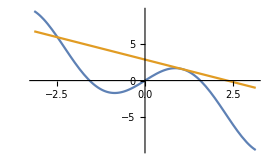

```mathematica
Plot[{f[x], f'[π/3](x-π/3)+f[π/3]}, {x, -Pi, Pi}]
```

3 - Find where there is a horizontal tangent on

```mathematica
f[x_]:=Sin[x]/(2+Cos[x])
```

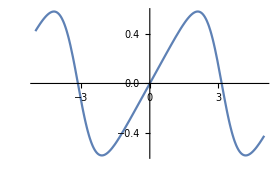

```mathematica
Plot[f[x], {x, -5, 5}]
```

```mathematica
Reduce[{f'[x] == 0, -5<=x≤5}]
```

x==-(4 π)/3||x==-(2 π)/3||x==(2 π)/3||x==(4 π)/3

4 - Find where speed of spring is greatest and where it is furthest from equilibrium on range 0 ≤ t ≤ 10

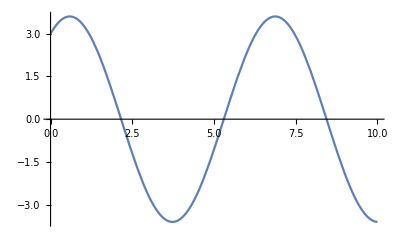

```mathematica
spring[t_]:=3 Cos[t]+2 Sin[t]
Plot[spring[x], {x, 0, 10}]
```

Find where velocity is zero

```mathematica
NSolve[spring'[x] ==0&& 0 ≤ x ≤ 10, x]
{spring'[x] ==0, 0 ≤ x ≤ 10} // Reduce // N
```

{{x→0.588003},{x→3.7296},{x→6.87119}}

x==3.7296||x==0.588003||x==6.87119

Find where acceleration is zero; also is where position is zero

```mathematica
NSolve[spring''[x] ==0&& 0 ≤ x ≤ 10, x]
{spring''[x] ==0, 0 ≤ x ≤ 10} // Reduce // N
```

{{x→2.1588},{x→5.30039},{x→8.44198}}

x==5.30039||x==2.1588||x==8.44198

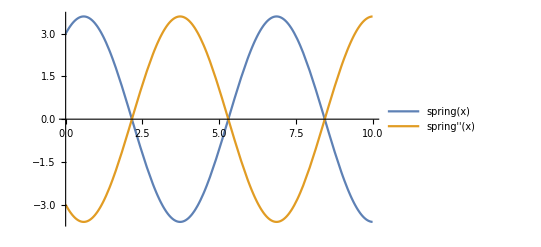

```mathematica
Plot[{spring[x],  spring''[x]}, {x, 0, 10}, PlotLegends->"Expressions"]
```

5 - Find where the rate of change of force is zero on 0 ≤ θ ≤ 2π and plot

```mathematica
w=100;μ=0.4;
force[θ_]:=μ w/(μ Sin[θ]+Cos[θ])
```

```mathematica
{force'[θ] == 0, 0 ≤ θ ≤ 2π} // Reduce // Quiet
```

θ==0.380506||θ==3.5221

## Demidovich exercises

#### 916- Graph the functions and determine domain, discontinuities, extremal points, intervals of increase and decrease, points of inflection, and the asymptotes.

We start with an example in the book.

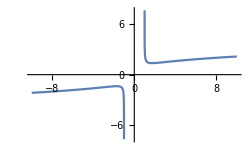

```mathematica
Plot[, {x, -10, 10}]
```

```mathematica
FunctionDomain[x/((x^2-1)^(1/3)),x]
```

x<-1||x>1

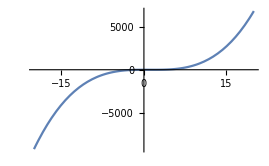

```mathematica
Plot[x^3-3 x^2,{x,-20,20}]
```